```mathematica
Clear["Global`*"]
(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

(*Define convencience function for plotting Gerschgorin’s disc of complex numbers *)
GerschgorinDisk[data_]:=Show[ListPlot[{Re[#],Im[#]}&/@data,AxesOrigin->{0,0},PlotRange->{{-0.5,0.5},{-0.5,0.5}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{Im,Re},PlotStyle->Directive[Red,PointSize[.05]]],Graphics@Circle[{0,0},1]]
```

```mathematica
(* MacArthur Rosenzweig consumer-reource model *)
fdRdt[Κ_,h_]=dRdt=r R (1-R/Κ)-a R C/(1+a h R)
fdCdt[Κ_,h_]=dCdt=e a R C/(1+a h R)-d C
```

-(a C R)/(1+a h R)+r R (1-R/Κ)

-C d+(a C e R)/(1+a h R)

```mathematica
fdRdt[10,2]
```

r (1-R/10) R-(a C R)/(1+2 a R)

```mathematica
isoR=Solve[dRdt==0,C][[1,1]]
isoC=Solve[dCdt==0,R][[1,1]]
```

C→-(r (1+a h R) (R-Κ))/(a Κ)

R→d/(a (e-d h))

```mathematica
equil=Solve[{dRdt==0,dCdt==0},{R,C}];
equil//TableForm
```

R→0 | C→0
R→d/(a (e-d h)) | C→(e r (-d+a e Κ-a d h Κ))/(a^2 (e-d h)^2 Κ)
R→Κ | C→0

```mathematica
equil[[2]]
```

{R→d/(a (e-d h)),C→(e r (-d+a e Κ-a d h Κ))/(a^2 (e-d h)^2 Κ)}

```mathematica
(* Specify some paremeter values for plotting *)
(*subparms={a->0.5,r->1,e->1,d->0.5};*)
subparms={a->0.03,r->0.2,e->0.25,d->0.055};
```

```mathematica
fisoR[Κ_,h_]=isoR[[2]]/.subparms
fisoC[h_]=isoC[[2]]/.subparms
```

-(6.66667 (1+0.03 h R) (R-Κ))/Κ

1.83333/(0.25-0.055 h)

```mathematica
(* Define model again, formulated for simulation through time *)
SimdRdt={R'[t]==r R[t] (1-R[t]/Κ)-a R[t] P[t]/(1+a h R[t]),R[0]==1};
SimdPdt={P'[t]==e a R[t] P[t]/(1+a h R[t])-d P[t],P[0]==0.1};
```

```mathematica
Manipulate[
GraphicsGrid[{{

Plot[fisoR[κ,η],{R,0,100},PlotRange->{0,All},GridLines->{{fisoC[η]},None},AxesLabel->{"R","C"}], 

StreamPlot[{fdRdt[κ,η],fdCdt[κ,η]}/.subparms,{R,0,80},{C,0,30},FrameLabel-> {"R","C"},StreamScale->0.1],  
 Plot[Evaluate[{R[t],P[t]}/.First[NDSolve[{{SimdRdt,SimdPdt}/.Join[subparms,{Κ->κ,h->η}]},{R,P},{t,0,4000}]]],{t,0,4000},PlotRange->{0,All}]

}}],
{{κ,15,"K"},1,150,1},
{{η,3.5,"h"},0,8,0.5}]
```

```mathematica
(* Community matrix (Jacobian of population growth rates) *)
A=JacobianMatrix[{dRdt,dCdt},{R,C}];
Simplify[A]//MatrixForm
```

(r-(a C)/(1+a h R)^2-(2 r R)/Κ | -(a R)/(1+a h R)
(a C e)/(1+a h R)^2 | -d+(a e R)/(1+a h R))

```mathematica
Aeq=A/.equil[[2]]//FullSimplify;
Aeq//MatrixForm
```

(-(d r (e+d h+a h (-e+d h) Κ))/(a e (e-d h) Κ) | -d/e
r (e-d h-d/(a Κ)) | 0)

```mathematica
(* Trace and Determinant *)
Tr[Aeq]
Det[Aeq]
```

-(d r (e+d h+a h (-e+d h) Κ))/(a e (e-d h) Κ)

d r-(d^2 h r)/e-(d^2 r)/(a e Κ)

```mathematica
(* Trace and Determinant of coexistence equilibrium as functions of K and h *)
tr[Κ_,h_]=Tr[Aeq]/.subparms
det[Κ_,h_]=Det[Aeq]/.subparms
```

-(1.46667 (0.25+0.055 h+0.03 (-0.25+0.055 h) h Κ))/((0.25-0.055 h) Κ)

0.011-0.00242 h-0.0806667/Κ

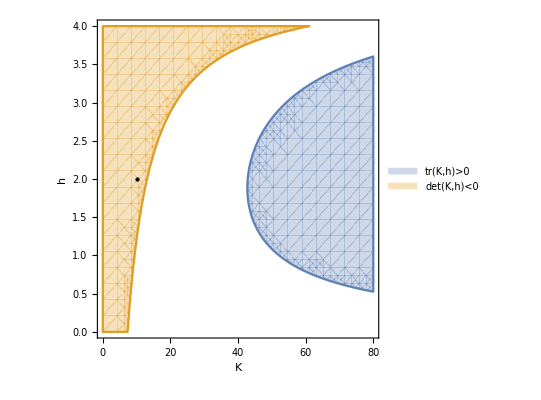

```mathematica
Show[RegionPlot[{tr[Κ,h]>0,det[Κ,h]<0},{Κ,0,80},{h,0,4},PlotLegends->"Expressions",FrameLabel->{"K","h"}],Graphics[{PointSize[Large],Point[{10,2}]}]]
```

```mathematica
(* Plot equality of Tr^2=4 Det ---> Tr = ±√(4 det)*)
Manipulate[
Row[{Show[RegionPlot[{tr[Κ,h]>0,det[Κ,h]<0},{Κ,0,80},{h,0,4},FrameLabel->{"K","h"}],Graphics[{PointSize[Large],Point[{Κ,h}]}]],Plot[{Sqrt[4d],-Sqrt[4d]},{d,-0.005,0.01},PlotRange->{-0.3,0.3},AxesLabel->{"Det","Tr"},Epilog->{PointSize[Large],Point[{det[Κ,h],tr[Κ,h]}]}]}],
{{Κ,40},1,150},
{{h,3.5},1,8}]
```

```mathematica
(* Eigenvalues of coexistence equilibrium *)
eig[Κ_,h_]=Eigenvalues[Aeq/.subparms];
```

```mathematica
Manipulate[
GraphicsGrid[
{{
Plot[fisoR[κ,η],{R,0,100},PlotRange->{0,All},GridLines->{{fisoC[η]},None},AxesLabel->{"R","C"}],

Plot[Evaluate[{R[t],P[t]}/.First[NDSolve[{{SimdRdt,SimdPdt}/.Join[subparms,{Κ->κ,h->η}]},{R,P},{t,0,4000}]]],{t,0,4000},PlotRange->{0,All}]

},{   

Plot[{Sqrt[4d],-Sqrt[4d]},{d,0,0.01},PlotRange->{-0.3,0.3},AxesLabel->{"Det","Tr"},Epilog->{PointSize[Large],Point[{det[κ,η],tr[κ,η]}]}],

GerschgorinDisk[eig[κ,η]]        
}
}],
{{κ,15,"K"},1,150,1},
{{η,3.5,"h"},0,8,0.5}]
```